# Portfolio Optimization

## Asset definitions

We define the assets that are going to be used. In this example, they were chosen among the top 10 performing stocks in S&P.

```mathematica
(*"AAPL","MSFT","AMZN","JNJ","XOM","JPM","GOOG"*)
(*"FAS","FIW","FYX","ERY","GEX","PSP"*)
portfolio={"AAPL","MSFT","AMZN","JNJ","XOM","JPM","GOOG"};
```

We get the pricing data by specifying 2010/01/01 as a starting date and then proceed to plot it.

```mathematica
data=FinancialData[#,"Close",{2010,1,1},"Value"]&/@portfolio;
```

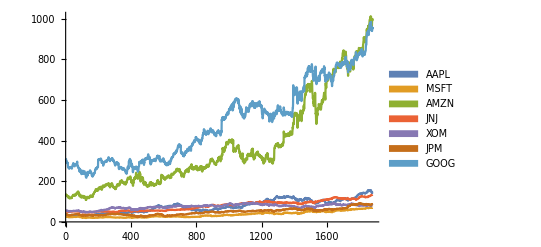

```mathematica
ListPlot[data,PlotRange->All,Joined->True,PlotLegends->SwatchLegend[portfolio]]
```

## Returns

What we are interested in are returns, that is, the percentage change of each asset price with respect to the one of the previous trading day.

```mathematica
getReturns[lst_]:=(lst[[#+1]]/lst[[#]])-1&/@Range[Length[lst]-1];
```

```mathematica
returns=getReturns[data[[#]]]&/@Range[Length[portfolio]];
```

Having calculated the returns with the defined function, we can proceed to plot the data.

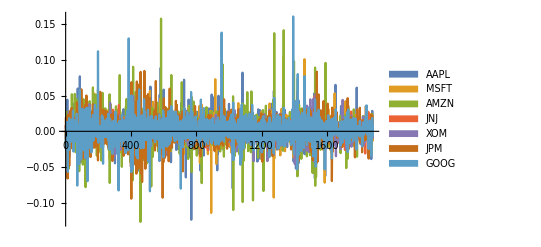

```mathematica
ListPlot[returns,PlotRange->All,Joined->True,PlotLegends->SwatchLegend[portfolio]]
```

## Optimization

Now that we have calculated returns, we can proceed to optimize our portfolio; that is, find a set of  weights (one for each asset) w, such that the expected risk of the portfolio is minimized for a given expected return. For this, we use modern portfolio theory, in particular, Markowitz optimization.

We can first define the weights vector as a symbolic object with the corresponding assets as subscripts.

```mathematica
weights=Transpose[{Subscript[w,#]&/@portfolio}]
```

{{w_AAPL},{w_MSFT},{w_AMZN},{w_JNJ},{w_XOM},{w_JPM},{w_GOOG}}

The expected return of our portfolio is given by R = ∑ m · w, where m is a row vector whose entries are given by the mean of each asset’s returns.

```mathematica
meanRet={Mean[#]&/@returns};
portfolioMean=Flatten[meanRet.weights][[1]]*252;
```

Next we calculate the variance of our portfolio, given by var = w^T · C · w, where C is the covariance matrix of the returns.

```mathematica
covMat=Covariance[Transpose[returns]];
portfolioVar=Flatten[Transpose[weights].covMat.weights][[1]]*252;
```

We multiply our results by 252 to consider annual returns, since there are approximately 252 business days in a year.

### Constraints

Having arranged our data, we need to specify some constraints on the optimization so that the result makes sense in a real investing environment, as well as to provide a way to personalize the optimization process. There are four basic constraints which one can be interested on:

∑_i w_i=1

w_i ≥ w_min

w_i ≤ w_max

R_exp ≥ R_min

The following function combines these constraints into a single constraint list, which we can then pass on to the optimization function.

```mathematica
constraints[wl_,wg_,retMin_]:=Union[
GreaterEqualThan[wl][#]&/@Flatten[Transpose[weights]],
LessEqualThan[wg][#]&/@Flatten[Transpose[weights]],
List[Total[weights][[1]]==1],
List[GreaterEqualThan[retMin][portfolioMean]]
];
```

The optimization consists of minimizing the portfolio variance for a given expected minimum return.

```mathematica
optPort[x_,y_,z_]:=NMinimize[{portfolioVar,constraints[x,y,z]},Flatten[weights]];
```

## Testing

In order to test the previous functions and concepts, we can optimize a portfolio for a given set of constraints. Lets say that every asset in our portfolio must take at least 5% of the total investment, and must not surpass 25%. Also, we are interested in finding the minimum variance portfolio, so we can set R_exp = 0.

```mathematica
mv=optPort[0.05, 0.25, 0.0]
```

{0.0217218,{w_AAPL→0.140277,w_MSFT→0.155247,w_AMZN→0.05,w_JNJ→0.25,w_XOM→0.25,w_JPM→0.05,w_GOOG→0.104476}}

This gave us the allocation weights for each asset, as well as the corresponding risk. For better control, we can group expected variance with expected returns as a row vector.

```mathematica
expRetRisk={Sqrt[mv[[1]]],portfolioMean /.mv[[2]]}
```

{0.147383,0.155645}

The following graph helps visualize the asset allocation for the minimum variance portfolio.

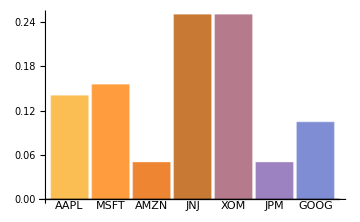

```mathematica
BarChart[{Last[mv[[2,#]]]&/@Range[Length[portfolio]]},ImageSize->Medium,ChartLabels->portfolio]
```

## Efficient Frontier

As a vital aspect of modern portfolio theory stands the concept of efficient frontier. Introduced my Harry Markowitz in the 50’s, this concept refers to the convex hull of every possible asset allocation for a given number of assets, that is, a given portfolio. This defines the optimal portfolio for every combination of expected risk and expected return.

In order to better visualize this concept, we can generate it by optimizing several portfolios, each uniquely determined by a distinct expected return.

```mathematica
effFrontier=Table[
{
NMinimize[
{
Sqrt[portfolioVar],
Union[
GreaterEqualThan[0.05][#]&/@Flatten[Transpose[weights]],
LessEqualThan[0.25][#]&/@Flatten[Transpose[weights]],
List[Total[weights][[1]]==1],
List[Equal[portfolioMean,i]]
]
},Flatten[weights]
][[1]],i
},{i,0.0,1,.001}];//Quiet
```

The following graph shows the efficient frontier for the past example of assets and constraints, along with several randomly generated portfolios. As an important remark, one should notice the red dot which represents the minimum variance portfolio found in the previous section.

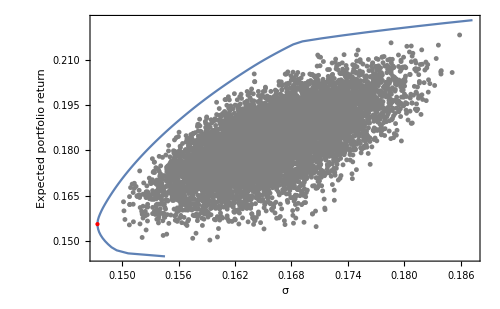

```mathematica
Show[
ListLinePlot[
effFrontier,Epilog->{Red,PointSize->Large,Point[expRetRisk]},Frame->True,FrameLabel->{"σ","Expected portfolio return"},PlotRange->{Automatic,Automatic},BaseStyle->14,ImageSize->500],
ListPlot[
Table[{Sqrt[portfolioVar],portfolioMean}/.Flatten[Select[{Thread[Flatten[Transpose[weights]]->#&[Normalize[RandomReal[{0.05,0.25},Length[portfolio]],Total]]]},AllTrue[#,0.05≤Last[#]≤0.25&]&]],{10000}],
PlotMarkers->{Automatic,5},PlotStyle->Gray]]//Quiet
```

## Backtesting

An important part of building models is to test them to analyze their performance on real scenarios. Lets build a backtesting function by specifying a window (time frame)

```mathematica
alloc=Last[mv[[2]][[#]]]&/@Range[Length[portfolio]]
```

{0.140277,0.155247,0.05,0.25,0.25,0.05,0.104476}

```mathematica
port=TimeSeriesThread[alloc.#&,data];
```

```mathematica
pc=PieChart[alloc,ChartLabels->Placed[Style[#,Small,Italic,FontFamily->"Helvetica"]&/@portfolio,"RadialCallout"],ColorFunction->"DarkBands",SectorOrigin->{{π/4,"Clockwise"},0},ChartStyle->Opacity[.6],ImageSize->200,ImagePadding->{{15,15},{0,0}}];
```

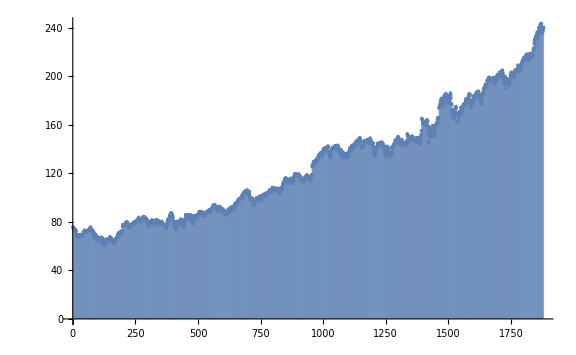

```mathematica
ListPlot[port,Filling->Axis,Epilog->Inset[pc,{500,175}],ImageSize->Large]
```

```mathematica
backtestShort[startDate_, window_,period_]:=Block[{data,endDate,ret,weights,meanRet,portfolioMean,covMat,portfolioVar,mv,alloc,futureData,port},(
Clear[data,endDate,ret,weights,meanRet,portfolioMean,covMat,portfolioVar,mv,alloc,futureData,port];
endDate=DayPlus[startDate,window*period,"BusinessDay"];
data = FinancialData[#,"Close",{startDate,endDate}]&/@portfolio;
ret=FinancialData[#,"FractionalChange",{startDate,endDate},"Value"]&/@portfolio;
weights=Transpose[{Subscript[w,#]&/@portfolio}];
meanRet={Mean[#]&/@ret};
portfolioMean=Flatten[meanRet.weights][[1]];
covMat=Covariance[Transpose[ret]];
portfolioVar=Flatten[Transpose[weights].covMat.weights][[1]];
mv=NMinimize[{portfolioVar,Union[
GreaterEqualThan[0.05][#]&/@Flatten[Transpose[weights]],
LessEqualThan[0.25][#]&/@Flatten[Transpose[weights]],
List[Total[weights][[1]]==1],
List[GreaterEqualThan[0.0][portfolioMean]]
]},
Flatten[weights]];;
alloc=Last[mv[[2]][[#]]]&/@Range[Length[portfolio]];
futureData= FinancialData[#,"Close",{endDate,DayPlus[endDate,window,"BusinessDay"]}]&/@portfolio;
List[mv[[2]]->TimeSeriesThread[alloc.#&,futureData]]
)];
```

```mathematica
portChart[port_]:=Block[{alloc},(
alloc=Last[port[[#]]]&/@Range[Length[portfolio]];
PieChart[alloc,ChartLabels->Placed[Style[#,Small,Italic,FontFamily->"Helvetica"]&/@portfolio,"RadialCallout"],ColorFunction->"DarkBands",SectorOrigin->{{π/4,"Clockwise"},0},ChartStyle->Opacity[.6],ImageSize->150,ImagePadding->{{15,15},{0,0}}]
)];
```

```mathematica
backtestLong[startDate_,window_,periods_]:=backtestShort[startDate,window,#]&/@Range[periods];
```

```mathematica
date=DateObject[{2011,1,1}];
wind=200;
period=5;
```

```mathematica
test=backtestLong[date,wind,period];
```

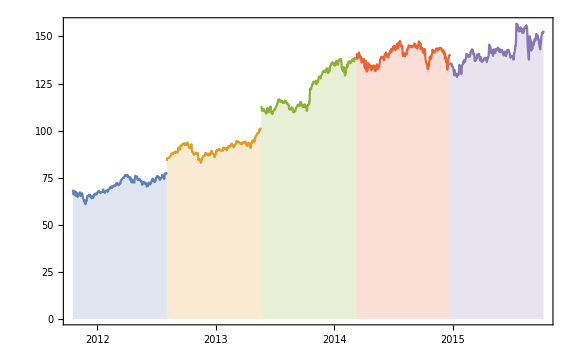

```mathematica
bla=Last[test[[#]][[1]]]&/@Range[period];
DateListPlot[bla,Filling->Axis,ImageSize->Large]
```

```mathematica
portfs=First[test[[#]][[1]]]&/@Range[5];
GraphicsGrid[Partition[portChart[portfs[[#]]]&/@Range[5],5],Frame->All]
```

-Graphics-